# Lecture 5

Q1:

```mathematica
f[x_]:=x*Exp[-x]+x*(1-x)
```

```mathematica
f[0]
f[0.1]
f[0.2]
f[0.4]
f[0.8]
```

0

0.180484

0.323746

0.508128

0.519463

Q2:

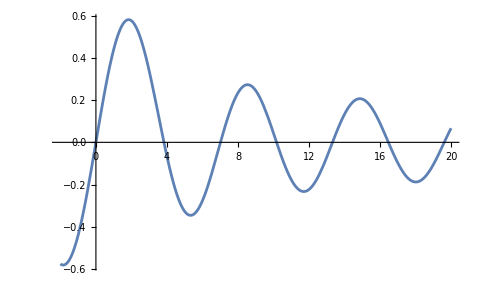

```mathematica
Plot[BesselJ[1,x],{x, -2,20}]
```

```mathematica
FindRoot[BesselJ[1,x]==0,{x,{0,3,6}}]
```

{x→{0.,3.83171,7.01559}}

Q3:

```mathematica
Integrate[Exp[-x]*Sin[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
D[%,x]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
Simplify[%]
```

ⅇ^-x Sin[x]